Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[{3/8+∑_(n=0)^20 ((Sin[(n π)/2] Cos[n π x])/(n π)+(Sin[(n π)/2] Cos[n π x])/(2 n π)),3/8+∑_(n=0)^80 ((Sin[(n π)/2] Cos[n π x])/(n π)+(Sin[(n π)/2] Cos[n π x])/(2 n π))} {x,-3,3},AxesLabel→{x,f(x,nmax)},PlotLegends→Expressions,PlotLabel→Junjie Wang,GridLines→Automatic,BaseStyle→{FontSize→18}]

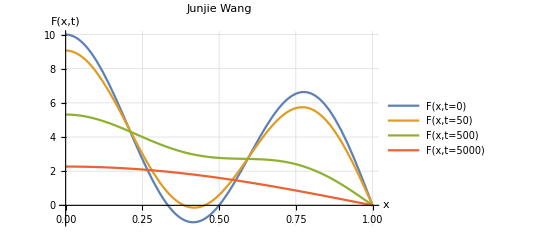

```mathematica
F[x_,t_]:=5Cos[Pi*x/2]*ⅇ^(-(Pi/2)^2*6.4*10^(-5)*t)+5Cos[5Pi*x/2]*ⅇ^(-(5Pi/2)^2*6.4*10^(-5)*t)
Plot[{F[x,t=0],F[x,t=50],F[x,t=500],F[x,t=5000]},{x,0,1},
AxesLabel-> {"x","F(x,t)"},
PlotLabel->"Junjie Wang",
PlotLegends->"Expressions",
GridLines->Automatic,
BaseStyle->{FontSize-> 18}]
```

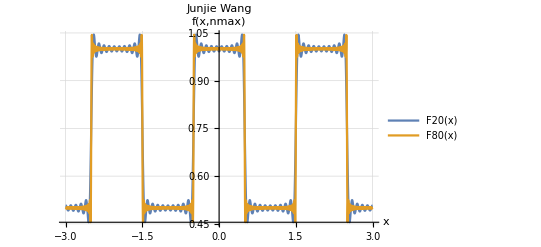

```mathematica
F20[x_]:={3/4+Sum[1/(n*Pi)*Sin[n*Pi/2]*Cos[n*Pi*x],{n,1,20}]}
F80[x_]:={3/4+Sum[1/(n*Pi)*Sin[n*Pi/2]*Cos[n*Pi*x],{n,1,80}]}
Plot[{F20[x],F80[x]},{x,-3,3},
AxesLabel-> {"x","f(x,nmax)"},
PlotLegends->"Expressions",
PlotLabel->"Junjie Wang",
GridLines->Automatic,
BaseStyle->{FontSize-> 18}]
```